```mathematica
SetDirectory[NotebookDirectory[]]
```

/ICFO/home/fcucchietti/Code/MathMPS

Load the library

```mathematica
<<MPS.m
```

MPS manipulation from Mathematica.
MPS Manipulation and creation:
	MPSProductState
	MPSExpandBond
	MPSNormalize
	MPSCanonize
Reading and saving to disk:
	MPSRead
	MPSSave
Expectation values:
	MPSExpectation
	MPSCorrelation
Algorithms:
	MPSApproximate
	MPSMinimizeEnergy
Hamiltonian Creation:
	MPSInitHamiltonian
	MPSHamiltonianAdd

Also available are TEBD algorithms:

Creation and disk interaction:
	TEBDProductState
	TEBDRead
	TEBDSave
Real and imaginary time evolution:
	TEBDEvolve
Expectation values:
	TEBDExpectation
	TEBDExpectationList
	TEBDentropy
	TEBDentropyList
Hamiltonians and evolution operators:
	TEBDInitHamiltonian
	TEBDHamiltonianAdd
	TEBDEvolutionFromHamiltonian
	TEBDInitEvolution
	TEBDEvolutionAddGate

Set some simulation parameters

```mathematica
bond=6; (* This will be the Bond Dimension *)
length=10; (* Length of the chain *)
intrange=1; (* Interaction range, 1 is nearest neighbor *)
μField = 0.10; (* Magnetic field *)
JCoupling=-1.0; (* Spin-spin coupling *)
```

We start by creating a random MPS.

```mathematica
mymps=MPSProductState[length,Bond->bond];
```

Normalization typically is optional, but it's a good habit

```mathematica
MPSNormalize[mymps];
```

The MPS is a nasty collection of matrices

```mathematica
mymps[[1]]//Normal
```

{{{0.0161366+0.0832834 ⅈ,-0.155314-0.0927526 ⅈ,0.254951-0.0491236 ⅈ,0.0234479-0.126735 ⅈ,-0.187273-0.0880815 ⅈ,-0.174709+0.0175192 ⅈ,0.185952-0.180756 ⅈ,-0.177761+0.0384222 ⅈ,-0.188848-0.0787133 ⅈ,0.193748-0.055941 ⅈ,-0.0620525+0.11348 ⅈ,0.0755084+0.248061 ⅈ,-0.137551+0.172877 ⅈ,-0.0788693-0.117921 ⅈ,0.0952363-0.0186162 ⅈ,0.142622+0.00300305 ⅈ,-0.199745+0.143211 ⅈ,-0.134223+0.125521 ⅈ,-0.14269+0.134879 ⅈ,-0.164046-0.0780676 ⅈ}},{{0.159627+0.195318 ⅈ,0.157544-0.115243 ⅈ,0.0199024-0.054928 ⅈ,-0.175282-0.153269 ⅈ,0.12166-0.114873 ⅈ,0.0748989-0.185436 ⅈ,0.0574719-0.0165166 ⅈ,0.140084+0.13464 ⅈ,-0.170179-0.00255292 ⅈ,-0.0907593-0.148059 ⅈ,0.190294+0.133741 ⅈ,0.0391374-0.0453747 ⅈ,0.0220366+0.146745 ⅈ,-0.0712004-0.213615 ⅈ,0.242345+0.0517574 ⅈ,0.204872+0.0922171 ⅈ,0.000137915+0.102074 ⅈ,0.0877944-0.171311 ⅈ,-0.170278+0.0572653 ⅈ,-0.186441-0.0553212 ⅈ}}}

```mathematica
Dimensions[mymps]
```

{10,2}

Now we need to create the Hamiltonian. For readability we define the axes names

```mathematica
Xaxis=1; Yaxis=2;Zaxis=3;
MyHamiltonian=MPSInitHamiltonian[length];
Do[
(* Add field terms *)
If[n==m,MPSHamiltonianAdd[MyHamiltonian,Xaxis,μField,n]];
(* Add nearest neighborg interaction *)
If[n==m+1,MPSHamiltonianAdd[MyHamiltonian,Zaxis,JCoupling,n,m]];,
{n,1,length},{m,1,length}]
```

Finally compute the ground state

```mathematica
energy=MPSMinimizeEnergy[mymps,MyHamiltonian,Verbose->False,Tolerance->10^(-7),Sweeps->6,MonitorEnergy->True,Debug->True]
```

{{-0.692971+0. ⅈ,-0.862282+0. ⅈ,-1.03901+0. ⅈ,-1.18457+0. ⅈ,-1.66376+0. ⅈ,«30»,-2.28009+0. ⅈ,-2.28009+0. ⅈ,-2.28009+0. ⅈ,-2.28009+0. ⅈ,-2.28009+0. ⅈ},{«1»}}

The state has changed.

```mathematica
mymps[[1]]//Normal
```

{{{0.0814673+0.622317 ⅈ,-0.0422775-0.322951 ⅈ}},{{-0.0814673-0.622317 ⅈ,-0.0422775-0.322951 ⅈ}}}

Now improve precision by making a larger bond MPS. You can ask for help on specific commands like in Mathematica

```mathematica
?MPSExpandBond
```

MPSExpandBond[mps,newχ] expands the bond dimension χ of mps to newχ. Returns the expanded mps as a new variable

```mathematica
MPSExpandBond[mymps,15];
```

Grow χ to 15

```mathematica
Newenergy=MPSMinimizeEnergy[mymps,MyHamiltonian,Verbose->False,Tolerance->10^(-5),Sweeps->5]
```

-2.52892+0. ⅈ

Measure something

```mathematica
?MPSExpectation
```

MPSExpectation[mps,operator,site]
MPSExpectation[mps,operator,site1,site2]
MPSExpectation[mps,operator1,site1,operator2,site2]

Computes the expectation value of one or two Hermitian operators acting on one or two sites

Let us define some operators to make it clean

```mathematica
X={{0.0,1.0},{1.0,0.0}};
Y={{0.0,-I 1.0},{I 1.0,0.0}};
Z={{1.0,0.0},{0.0,-1.0}};
Id={{1.0,0.0},{0.0,1.0}};
```

```mathematica
MPSExpectation[mymps,X,5]
```

-0.324021

A correlation can be directly plotted

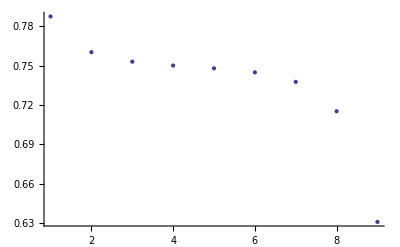

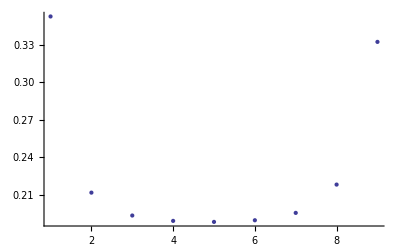

```mathematica
ListPlot[MPSCorrelation[mymps,Z,1,Z,10]]
ListPlot[MPSCorrelation[mymps,X,1,X,10]]
```

## TEBD Example

We will use the same parameters as above

```mathematica
bond=8; (* This will be the Bond Dimension *)
length=10; (* Length of the chain *)
intrange=1; (* Interaction range, 1 is nearest neighbor *)
μField = 0.3; (* Magnetic field *)
JCoupling=1.0; (* Spin-spin coupling *)
```

```mathematica
?TEBDProductState
```

TEBDProductState[numSites,Options]
Creates a TEBD representation state. 
Options:
	Spin→integer (Default is 2)
	BondDimension→integer   (default is 20)
	Type→{type,list}     (Creates several types of TEBDs: type="Random" , "Identity", or "Specified".
						If Specified is chosen, then list must be a Table of dimensions {numSites,2}, containing in each element a pair {probAmplitude,phase}

```mathematica
mytebd=TEBDProductState[10,BondDimension->15];
```

To create the Hamiltonian we must keep in mind that the order in which the operators are added imposes the sequence in which they are implemented later in the evolution operator. In principle we can also create an evolution operator directly, which gives us even more control since we can do periodic boundary conditions or long range interactions. The control is primitive but powerful, however in the future I expect to come up with some algorithm that finds some optimal evolution operator automatically.

For now, let us see how we can make the evolution operator with imaginary time of the same system but with periodic boundary conditions. We have to first initialize

```mathematica
U=TEBDInitEvolution[];
```

```mathematica
δt=-I 0.01;
ZZ=KroneckerProduct[Z,Z];
```

We will do a Trotter-Suzuki evolution of second order. For this, we first add evolution gates to the odd bonds for a time δt/2

```mathematica
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling ZZ/2],i,i+1],
{i,1,9,2}]
```

Now the even bonds

```mathematica
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling ZZ/2],i,i+1],
{i,2,8,2}]
```

The end-to-end coupling needs to be done by swapping the first and last spins until they are next to each other. For this, we add a bunch of swap operations

```mathematica
(SWAP={{1.0,0.0,0.0,0.0},{0.0,0.0,1.0,0.0},{0.0,1.0,0.0,0.0},{0.0,0.0,0.0,1.0}})//MatrixForm
```

(1. | 0. | 0. | 0.
0. | 0. | 1. | 0.
0. | 1. | 0. | 0.
0. | 0. | 0. | 1.)

```mathematica
Do[
TEBDEvolutionAddGate[U,SWAP,i,i+1],
{i,1,8}]
```

Now make them interact

```mathematica
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling ZZ/2],9,10];
```

And bring it back to where it was

```mathematica
Do[
TEBDEvolutionAddGate[U,SWAP,i,i+1],
{i,8,1,-1}]
```

Now we add the field terms to all the sites

```mathematica
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt μField X],i],
{i,1,10,1}]
```

To complete the second order Trotter-Suzuki, we need to add the same gates but in transposed order

```mathematica
Do[
TEBDEvolutionAddGate[U,SWAP,i,i+1],
{i,1,8}];
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling ZZ/2],9,10];
Do[
TEBDEvolutionAddGate[U,SWAP,i,i+1],
{i,8,1,-1}];
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling ZZ/2],i,i+1],
{i,2,8,2}];
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling ZZ/2],i,i+1],
{i,1,9,2}];
```

```mathematica
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling ZZ/2],i,i+1],
{i,2,8,2}];
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling ZZ/2],i,i+1],
{i,1,9,2}];
```

We have a total of

```mathematica
Length[U]
```

28

gates per evolution step (the swaps add a lot of work).

Let us see if it works by applying this 1000 times...

```mathematica
error=TEBDEvolve[mytebd,U,1000,Verbose->True]
```

-176.823

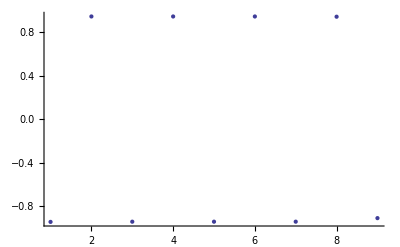

```mathematica
ListPlot[TEBDExpectationList[mytebd,1,10,Z,Z]]
```

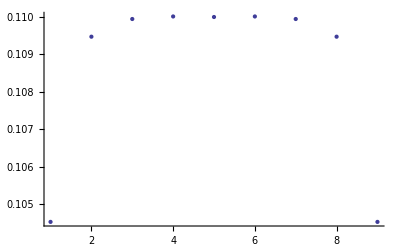

```mathematica
ListPlot[TEBDEntropyList[mytebd]]
```

Overlaps can be calculated by the expectation value of Identity...maybe I will improve this later

```mathematica
TEBDExpectation[mytebd,1,Id]
```

1.

```mathematica
IsLinkActive
```

IsLinkActive